## net

```mathematica
net=NetChain[
{
(*Implicit LinearLayer[1]*) 
LinearLayer[1],
Ramp,
LinearLayer[10],
Tanh,
LinearLayer[10],
Ramp,
LinearLayer[10],
Tanh,
LinearLayer[10],
Ramp,

LinearLayer[1]
},
"Input"->"Scalar",
"Output"->"Scalar"]
```

NetChain[<>]

```mathematica
data=Table[x->(Sin[10x]*Exp[-x^2]+x),{x,-3,3,.02}];
plotData[points_,color_]:=ListPlot[points,PlotStyle->color,FrameTicks->False,PlotRangePadding->0.1,Frame->True,PlotRange->All];
plot=plotData[data[[All,2]],GrayLevel[0.7]];
plotSolution[net_,t_]:=Show[plot,plotData[net@Range[-3,3,.02],Red],Epilog->Text[t,{10,0.9},{-1,0}]]
```

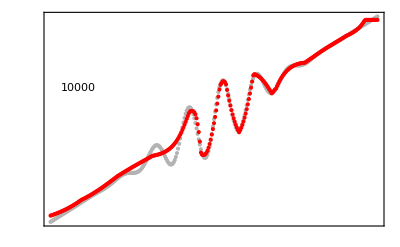

```mathematica
trained=NetTrain[net,data,
Method->{"SGD","LearningRate"->0.01},
TargetDevice->{"GPU",3},
MaxTrainingRounds->Quantity[20,"Seconds"],TrainingProgressReporting->{plotSolution[#Net,#AbsoluteBatch]&,"Interval"->0.1}];
plotSolution[trained,10000]
```